## Loading MathTIDES

```mathematica
<<MathTIDES`
```

MathTIDES 2.00
    MathTIDES    is   part   of   the   TIDES   project.
    Copyright(C)  2010  Abad, A.,  Barrio, R.,  Blesa, F.  and  Rodriguez, M.

## Setting the work directory

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/abad/Desktop/TIDESExamples/tutorial06

## Declaring the three body problem differential equation

```mathematica
threeBP={x''-2 y'==x-(1-mu) (x+mu)/r^3-mu (x+mu-1)/s^3,y''+2 x'==y-(1-mu) y/r^3-mu y/s^3
}/.{r->Sqrt[(x+mu)^2+y^2],s->Sqrt[(x+mu-1)^2+y^2]}
```

{-2 y'+x''==x-(mu (-1+mu+x))/(((-1+mu+x)^2+y^2)^(3/2))-((1-mu) (mu+x))/(((mu+x)^2+y^2)^(3/2)),2 x'+y''==y-(mu y)/(((-1+mu+x)^2+y^2)^(3/2))-((1-mu) y)/(((mu+x)^2+y^2)^(3/2))}

```mathematica
threeBPEQ = NthOrderODE[threeBP, t, {x,y},{mu}]
```

FirstOrderODE$[{x$d1,y$d1,x-(mu (-1+mu+x))/(((-1+mu+x)^2+y^2)^(3/2))-((1-mu) (mu+x))/(((mu+x)^2+y^2)^(3/2))+2 y$d1,-2 x$d1+y-(mu y)/(((-1+mu+x)^2+y^2)^(3/2))-((1-mu) y)/(((mu+x)^2+y^2)^(3/2))},t,{x,y,x$d1,y$d1},{mu}]

## Writing the integrator

```mathematica
TSMCodeFiles[threeBPEQ, 
"threebody", 
InitialConditions->{0.85,0.5,0,0},
ParametersValue->{0.001},
IntegrationPoints->{0, 150, Points[150]},
Output->"horseshoe"]
```

Files "dr_threebody.c", "threebody.h", threebody.c", "dp_tides.h", written on directory "/Users/abad/Dropbox/Trabajo/TidesWork/EjemplosTutorial/trescuerpos".

## Checking the solution

### Reading the file

```mathematica
dat = OpenRead["horseshoe"]
```

InputStream[horseshoe,15]

```mathematica
sol= ReadList[dat, {Real, Real, Real, Real, Real}];
```

### Taking the coordinates x, y of the solution

```mathematica
solxy = Map[{#[[2]],#[[3]]}&, sol];
```

### Ploting the solution

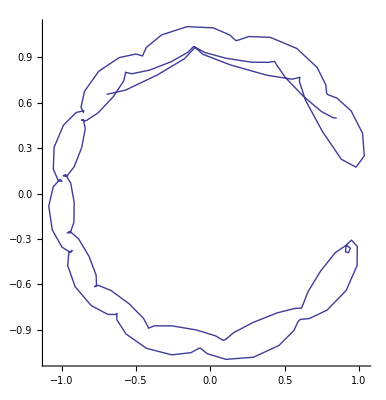

```mathematica
ListPlot[solxy, Joined->True, AspectRatio->Automatic]
```

```mathematica
Close[dat]
```

horseshoe